```mathematica
ClearAll["Global`*"];
```

```mathematica
(* ====================================================== *)
(* 1. Geometry and simulation parameters                  *)
(* ====================================================== *)

d = 5.0;                 (* photodiode thickness in microns *)
zGenMax = 2.0;           (* holes only generated between z=0 and z=2 microns *)
pitch = 10.0;             (* anode pitch in microns *)
nCharges = 5;            (* number of holes to simulate *)

(* Simulated lateral volume boundaries *)
xMin = -1.5 pitch;
xMax =  1.5 pitch;
yMin = -1.5 pitch;
yMax =  1.5 pitch;
zMin = 0.0;
zMax = d;

xyRange = {xMin, xMax};

(* 3x3 anode centers in the plane z = d *)
anodeCoords = Flatten[
   Table[{i pitch, j pitch, d}, {j, -1, 1}, {i, -1, 1}],
   1
];

nAnodes = Length[anodeCoords];
anodeLabels = Table["A" <> ToString[k], {k, nAnodes}];

(* ====================================================== *)
(* 2. Toy electrostatic-like model parameters             *)
(* ====================================================== *)

u0 = 1.0;                (* baseline well strength *)
z0 = 0.6;                (* softening length in microns *)
Teff = 0.25;             (* effective temperature / stochasticity *)
beta = 0.18;             (* how strongly collected charge weakens the well *)
uFloor = 0.15;           (* minimum well strength *)

useLossChannel = False;
Uloss = -0.25;           (* less attractive than most anodes *)

(* ====================================================== *)
(* 3. Hole generation                                     *)
(* ====================================================== *)

(* Restrict initial hole creation to the simulation volume,
   with z constrained to [0, 2] microns *)
sampleGenerationPoint[] := Module[{x, y, z},
  x = RandomReal[{xMin, xMax}];
  y = RandomReal[{yMin, yMax}];
  z = RandomReal[{0, zGenMax}];
  {x, y, z}
];
```

```mathematica
(* ====================================================== *)
(* 4. State variables and potential model                 *)
(* ====================================================== *)

Qstate0 = ConstantArray[0, nAnodes];

(* Effective well strengths from collected charge *)
uFromQ[Q_List] := Map[
   Max[uFloor, u0 - beta #] &,
   Q
];

(* Potential from one anode k *)
singlePotential[{x_, y_, z_}, k_, Q_List] := Module[
  {uk, ak, dx, dy, dz},
  uk = uFromQ[Q][[k]];
  ak = anodeCoords[[k]];
  dx = x - ak[[1]];
  dy = y - ak[[2]];
  dz = z - ak[[3]];
  -uk/Sqrt[dx^2 + dy^2 + dz^2 + z0^2]
];

(* Total potential *)
totalPotential[{x_, y_, z_}, Q_List] := Total[
  Table[singlePotential[{x, y, z}, k, Q], {k, 1, nAnodes}]
];

(* Landing weights from single-anode wells *)
landingWeights[{x_, y_, z_}, Q_List] := Module[
  {Uk},
  Uk = Table[singlePotential[{x, y, z}, k, Q], {k, 1, nAnodes}];
  Exp[-Uk/Teff]
];

landingProbabilities[pos_, Q_List] := Module[
  {w, allw},
  w = landingWeights[pos, Q];
  If[useLossChannel,
    allw = Join[w, {Exp[-Uloss/Teff]}];
    allw/Total[allw],
    w/Total[w]
  ]
];

sampleLanding[pos_, Q_List] := Module[
  {p, choiceSpace},
  p = landingProbabilities[pos, Q];
  choiceSpace = If[useLossChannel, Join[Range[nAnodes], {"Loss"}], Range[nAnodes]];
  RandomChoice[p -> choiceSpace]
];

(* Final position of a hole:
   if collected, its final point is the anode center;
   if lost, keep it at initial point for visualization. *)
finalHolePosition[initialPos_, picked_] := Module[{},
  If[picked === "Loss",
    initialPos,
    anodeCoords[[picked]]
  ]
];

(* ====================================================== *)
(* 5. 3D visualization helpers                            *)
(* ====================================================== *)

anodeGraphics3D[] := Graphics3D[{
   Black, PointSize[0.022], Point[anodeCoords],
   Table[
     Text[
       Style[anodeLabels[[k]], 12, Bold, Black],
       anodeCoords[[k]] + {0.35, 0.35, 0.0}
     ],
     {k, nAnodes}
   ]
}];

holeGraphics3D[initialPos_:None, finalPos_:None, picked_:None] := Graphics3D[
  {
    If[initialPos === None, {},
      {
        Red, PointSize[0.03], Point[initialPos],
        Text[
          Style["initial", 13, Bold, Red],
          initialPos + {0.45, 0.45, 0.0}
        ]
      }
    ],

    If[finalPos === None, {},
      {
        Blue, PointSize[0.03], Point[finalPos],
        Text[
          Style[
            If[picked === "Loss", "final (loss)", "final"],
            13, Bold, Blue
          ],
          finalPos + {0.45, -0.45, 0.0}
        ]
      }
    ],

    If[initialPos === None || finalPos === None, {},
      {
        Directive[Purple, Thick, Dashed],
        Line[{initialPos, finalPos}]
      }
    ]
  }
];

volumeBoundaryGraphics3D[] := Graphics3D[
  {
    Directive[Gray, Thick, Opacity[0.25]],
    Cuboid[{xMin, yMin, zMin}, {xMax, yMax, zMax}]
  },
  Boxed -> False
];

generationSlabGraphics3D[] := Graphics3D[
  {
    Directive[Orange, Opacity[0.12]],
    Cuboid[{xMin, yMin, 0.0}, {xMax, yMax, zGenMax}],
    Text[
      Style["generation region: 0 ≤ z ≤ 2 μm", 12, Bold, Darker[Orange]],
      {xMin + 1.7, yMin + 1.0, zGenMax + 0.25}
    ]
  },
  Boxed -> False
];

potentialPlot3D[Q_List, initialPos_:None, finalPos_:None, picked_:None] := Module[
  {basePlot, combinedPlot, legend},

  basePlot = DensityPlot3D[
    totalPotential[{x, y, z}, Q],
    {x, xMin, xMax},
    {y, yMin, yMax},
    {z, zMin, zMax},
    PlotPoints -> 16,
    ColorFunction -> "SolarColors",
    ColorFunctionScaling -> True,
    BoxRatios -> {1, 1, 0.6},
    AxesLabel -> {"x (μm)", "y (μm)", "z (μm)"},
    PlotLabel -> "3D total potential landscape",
    ImageSize -> 550,
    PerformanceGoal -> "Quality"
  ];

  combinedPlot = Show[
    basePlot,
    volumeBoundaryGraphics3D[],
    generationSlabGraphics3D[],
    anodeGraphics3D[],
    holeGraphics3D[initialPos, finalPos, picked]
  ];

  legend = BarLegend[
    {"SolarColors", MinMax@Table[
        totalPotential[{xx, yy, zz}, Q],
        {xx, xMin, xMax, (xMax - xMin)/8},
        {yy, yMin, yMax, (yMax - yMin)/8},
        {zz, zMin, zMax, (zMax - zMin)/6}
      ] // Flatten},
    LabelStyle -> 12,
    LegendLabel -> Style["Total potential U(x,y,z)", 12]
  ];

  Legended[combinedPlot, Placed[legend, Right]]
]
probabilityMap3DForAnode[k_, Q_List, initialPos_:None, finalPos_:None, picked_:None] := Module[
  {basePlot, combinedPlot, legend},

  basePlot = DensityPlot3D[
    landingProbabilities[{x, y, z}, Q][[k]],
    {x, xMin, xMax},
    {y, yMin, yMax},
    {z, zMin, zMax},
    PlotPoints -> 16,
    ColorFunction -> "SunsetColors",
    ColorFunctionScaling -> True,
    BoxRatios -> {1, 1, 0.6},
    AxesLabel -> {"x (μm)", "y (μm)", "z (μm)"},
    PlotLabel -> Row[{"3D landing probability field for ", anodeLabels[[k]]}],
    ImageSize -> 550,
    PerformanceGoal -> "Quality"
  ];

  combinedPlot = Show[
    basePlot,
    volumeBoundaryGraphics3D[],
    generationSlabGraphics3D[],
    anodeGraphics3D[],
    holeGraphics3D[initialPos, finalPos, picked]
  ];

  legend = BarLegend[
    {"SunsetColors", {0, 1}},
    LabelStyle -> 12,
    LegendLabel -> Style[Row[{"Landing probability for ", anodeLabels[[k]]}], 12]
  ];

  Legended[combinedPlot, Placed[legend, Right]]
]

(* 2D slice retained because it is still very useful diagnostically *)
potentialPlotAtDepth[zSlice_, Q_List, initialPos_:None, finalPos_:None] := Module[
  {basePlot, legend, vals},

  vals = Flatten@Table[
     totalPotential[{x, y, zSlice}, Q],
     {x, xMin, xMax, (xMax - xMin)/30},
     {y, yMin, yMax, (yMax - yMin)/30}
  ];

  basePlot = DensityPlot[
    totalPotential[{x, y, zSlice}, Q],
    {x, xMin, xMax}, {y, yMin, yMax},
    PlotPoints -> 45,
    MaxRecursion -> 1,
    ColorFunction -> "SolarColors",
    ColorFunctionScaling -> True,
    FrameLabel -> {"x (μm)", "y (μm)"},
    PlotLabel -> Row[{"2D slice of total potential at z = ", NumberForm[zSlice, {3, 2}], " μm"}],
    Epilog -> {
      Black, PointSize[0.02], Point[anodeCoords[[All, 1 ;; 2]]],
      Table[
        Text[Style[anodeLabels[[k]], 12, Bold, Black], anodeCoords[[k, 1 ;; 2]] + {0.3, 0.3}],
        {k, nAnodes}
      ],
      If[initialPos === None, {},
        {
          Red, PointSize[0.025], Point[initialPos[[1 ;; 2]]],
          Text[Style["initial", 13, Bold, Red], initialPos[[1 ;; 2]] + {0.35, -0.35}]
        }
      ],
      If[finalPos === None, {},
        {
          Blue, PointSize[0.025], Point[finalPos[[1 ;; 2]]],
          Text[Style["final", 13, Bold, Blue], finalPos[[1 ;; 2]] + {0.35, 0.35}]
        }
      ]
    },
    ImageSize -> 500
  ];

  legend = BarLegend[
    {"SolarColors", MinMax[vals]},
    LabelStyle -> 12,
    LegendLabel -> Style["Total potential on z-slice", 12]
  ];

  Legended[basePlot, Placed[legend, Right]]
]

barProbabilities[pos_, Q_List] := Module[
  {p, labels},
  p = landingProbabilities[pos, Q];
  labels = If[useLossChannel, Join[anodeLabels, {"Loss"}], anodeLabels];
  BarChart[
    p,
    ChartLabels -> Placed[labels, Below],
    PlotRange -> {0, 1},
    Frame -> True,
    FrameLabel -> {"destination", "probability"},
    PlotLabel -> "Landing probabilities at this initial hole position",
    ImageSize -> 550
  ]
];

anodeStrengthBar[Q_List] := Module[
  {uvals},
  uvals = uFromQ[Q];
  BarChart[
    uvals,
    ChartLabels -> Placed[anodeLabels, Below],
    Frame -> True,
    FrameLabel -> {"anode", "well strength u_k"},
    PlotLabel -> "Current effective well strengths",
    ImageSize -> 550
  ]
];

chargeBar[Q_List] := BarChart[
  Q,
  ChartLabels -> Placed[anodeLabels, Below],
  Frame -> True,
  FrameLabel -> {"anode", "collected holes"},
  PlotLabel -> "Collected charge per anode",
  ImageSize -> 550
];

chargeHistoryPlot[Qhist_List] := Module[
  {series},
  series = Transpose[Qhist];
  ListLinePlot[
    series,
    PlotMarkers -> Automatic,
    Frame -> True,
    FrameLabel -> {"step", "Q_k"},
    PlotLabel -> "Charge history of the 9 anodes",
    PlotLegends -> anodeLabels,
    ImageSize -> 650
  ]
];

(* Optional: show the initial z-values of generated holes *)
holeDepthHistoryPlot[holePositions_List] := ListPlot[
  holePositions[[All, 3]],
  PlotMarkers -> Automatic,
  Frame -> True,
  FrameLabel -> {"hole index", "initial z (μm)"},
  PlotLabel -> "Initial generation depths of holes",
  PlotRange -> {0, zGenMax},
  ImageSize -> 500
];
```

```mathematica
(* ====================================================== *)
(* 6. Main stochastic simulation                          *)
(* ====================================================== *)

simulateOneRun[nSteps_Integer] := Module[
  {
    Q = Qstate0,
    Qhist = {Qstate0},
    holePositions = {},
    finalPositions = {},
    choices = {},
    probHist = {},
    report = {},
    pos, probs, picked, finalPos, representativeAnodeIndex
  },

  Do[
    pos = sampleGenerationPoint[];
    AppendTo[holePositions, pos];

    probs = landingProbabilities[pos, Q];
    AppendTo[probHist, probs];

    picked = sampleLanding[pos, Q];
    AppendTo[choices, picked];

    finalPos = finalHolePosition[pos, picked];
    AppendTo[finalPositions, finalPos];

    representativeAnodeIndex = If[
      picked === "Loss",
      First@Ordering[Most[probs], -1],
      picked
    ];

    AppendTo[report,
      <|
        "Step" -> Length[choices],
        "InitialPosition" -> pos,
        "FinalPosition" -> finalPos,
        "Probabilities" -> probs,
        "Choice" -> picked,
        "QBeforeUpdate" -> Q,
        "PotentialPlot3D" -> potentialPlot3D[Q, pos, finalPos, picked],
        "RepresentativeProbabilityPlot3D" -> probabilityMap3DForAnode[
          representativeAnodeIndex, Q, pos, finalPos, picked
        ],
        "PotentialSlice2D" -> potentialPlotAtDepth[pos[[3]], Q, pos, finalPos],
        "ProbabilityBarChart" -> barProbabilities[pos, Q],
        "StrengthBar" -> anodeStrengthBar[Q]
      |>
    ];

    If[picked =!= "Loss",
      Q[[picked]] = Q[[picked]] + 1;
    ];

    AppendTo[Qhist, Q];
    report[[-1, "QAfterUpdate"]] = Q;
    report[[-1, "ChargeBarAfter"]] = chargeBar[Q];
    ,
    {nSteps}
  ];

  <|
    "Report" -> report,
    "HolePositions" -> holePositions,
    "FinalPositions" -> finalPositions,
    "Choices" -> choices,
    "ProbabilityHistory" -> probHist,
    "QHistory" -> Qhist
  |>
];
```

Choices: {4,5,3,3,6}

Initial hole positions: {{11.2983,0.658928,0.172447},{-14.6507,12.818,1.08751},{-7.63952,7.79688,1.96999},{-1.22948,11.5419,1.16771},{12.5868,-2.28494,1.97458}}

Final hole positions: {{-10.,0.,5.},{0.,0.,5.},{10.,-10.,5.},{10.,-10.,5.},{10.,0.,5.}}

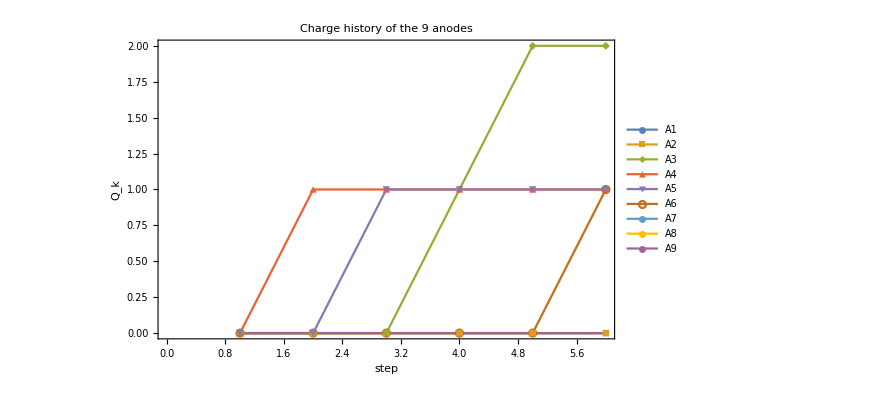

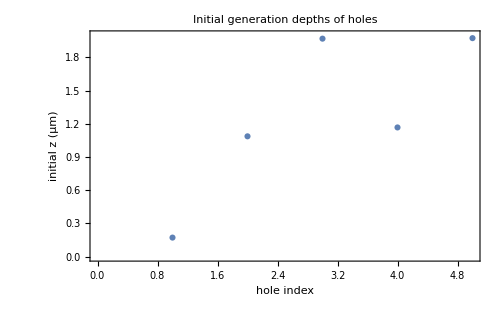

```mathematica
(* ====================================================== *)
(* 7. Run the simulation                                  *)
(* ====================================================== *)

SeedRandom[1234];
sim = simulateOneRun[nCharges];

(* ====================================================== *)
(* 8. Summary outputs                                     *)
(* ====================================================== *)

Print["Choices: ", sim["Choices"]];
Print["Initial hole positions: ", sim["HolePositions"]];
Print["Final hole positions: ", sim["FinalPositions"]];

Print[chargeHistoryPlot[sim["QHistory"]]];
Print[holeDepthHistoryPlot[sim["HolePositions"]]];
```

===== Charge 1 =====

Initial position (x, y, z) in microns: {11.2983,0.658928,0.172447}

Final position (x, y, z) in microns:   {-10.,0.,5.}

Choice: 4

-Graphics3D-

-Graphics3D-

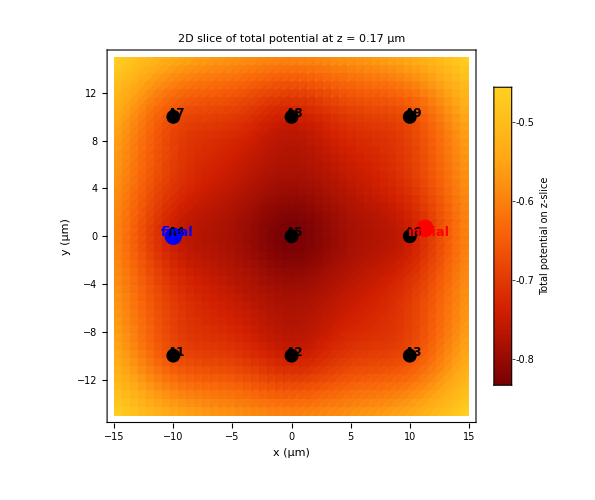

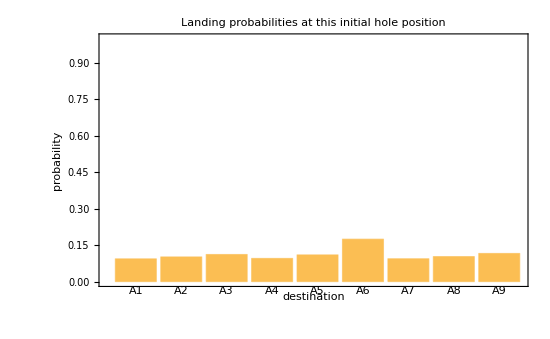

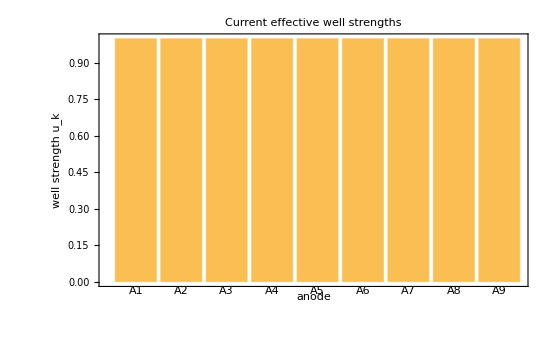

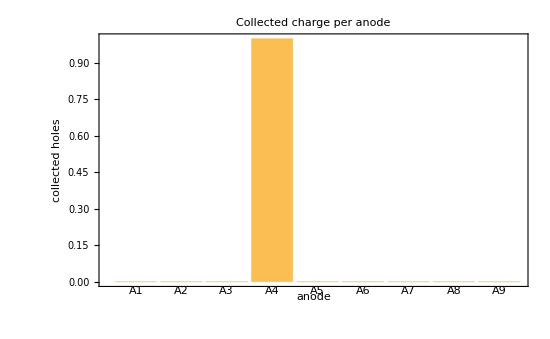

===== Charge 2 =====

Initial position (x, y, z) in microns: {-14.6507,12.818,1.08751}

Final position (x, y, z) in microns:   {0.,0.,5.}

Choice: 5

-Graphics3D-

-Graphics3D-

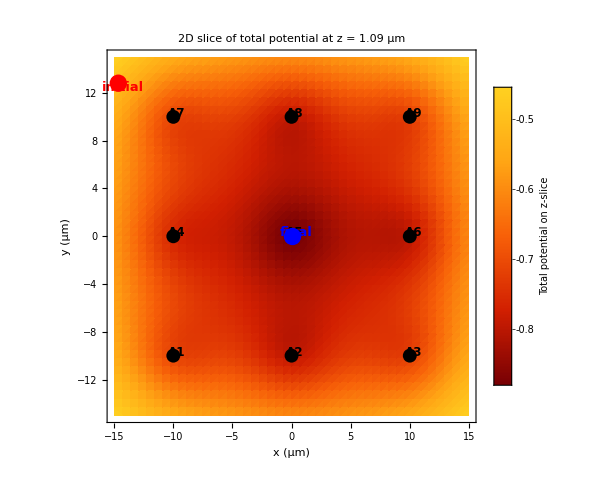

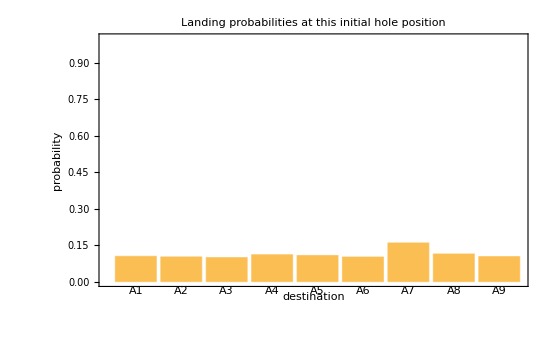

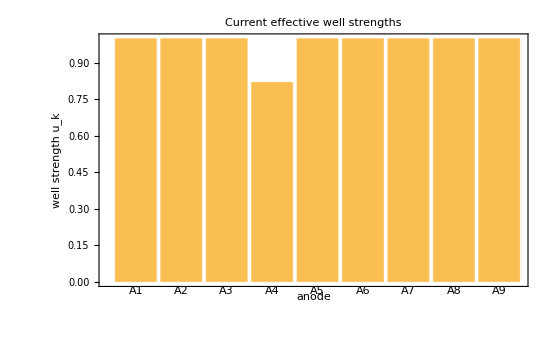

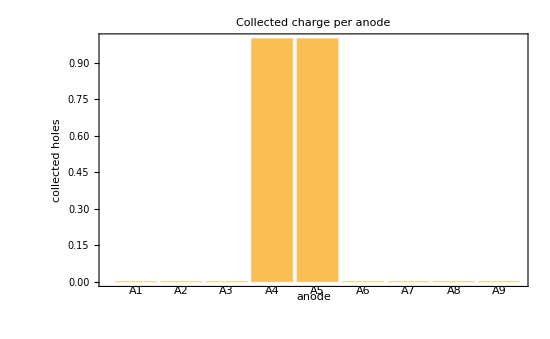

===== Charge 3 =====

Initial position (x, y, z) in microns: {-7.63952,7.79688,1.96999}

Final position (x, y, z) in microns:   {10.,-10.,5.}

Choice: 3

-Graphics3D-

-Graphics3D-

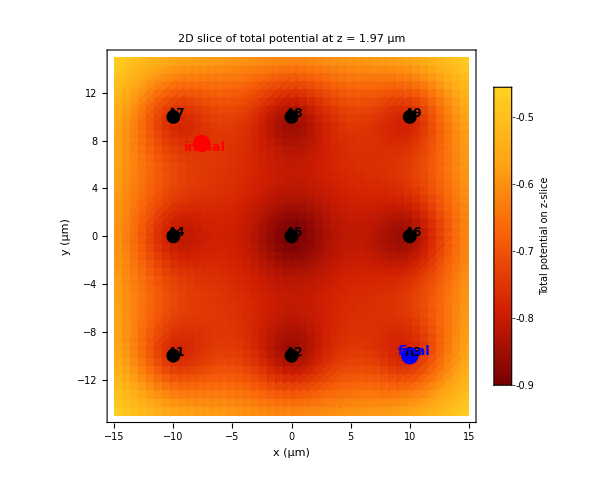

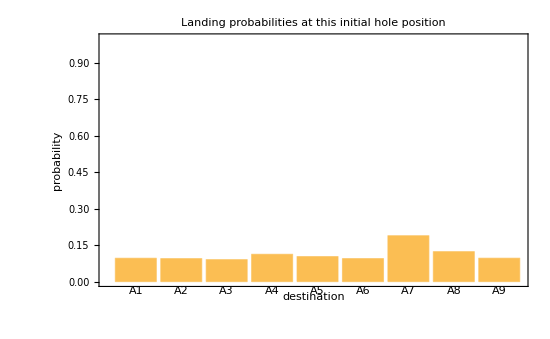

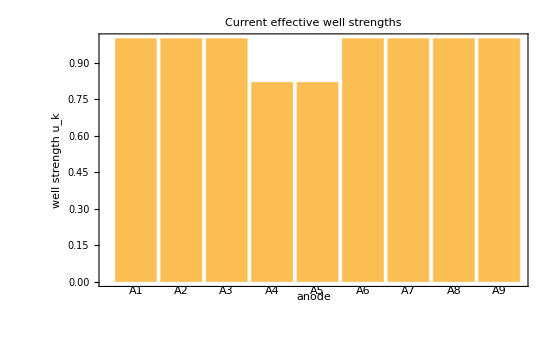

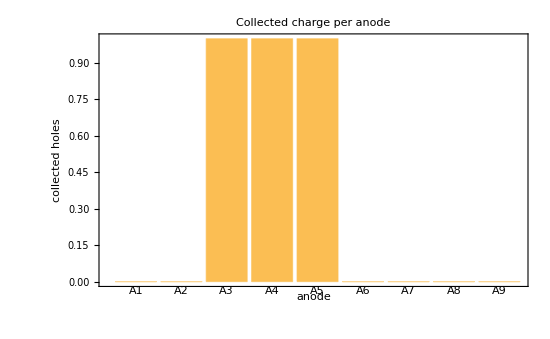

===== Charge 4 =====

Initial position (x, y, z) in microns: {-1.22948,11.5419,1.16771}

Final position (x, y, z) in microns:   {10.,-10.,5.}

Choice: 3

-Graphics3D-

-Graphics3D-

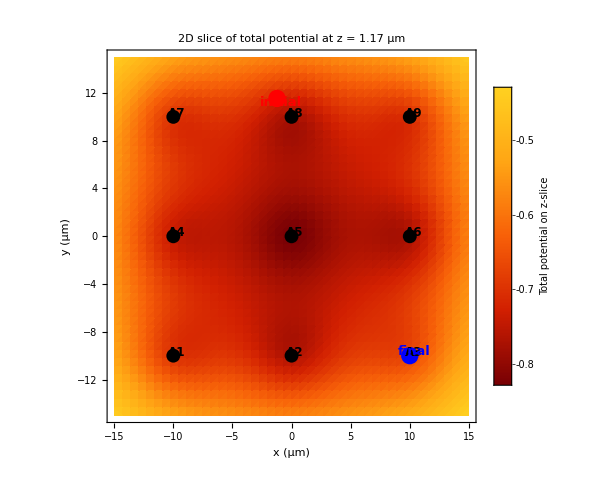

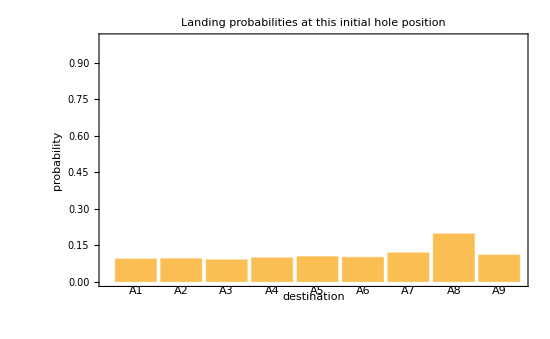

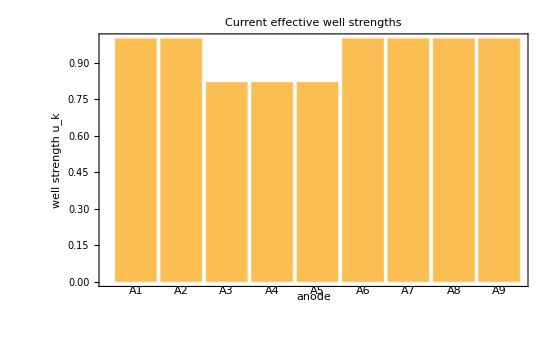

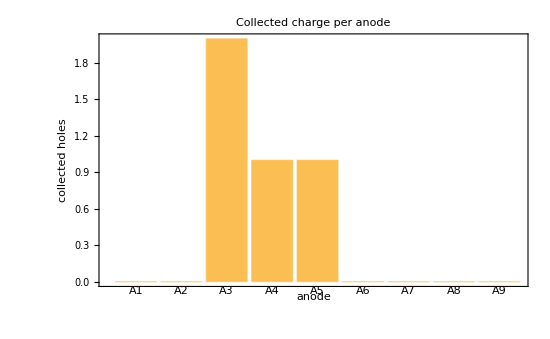

===== Charge 5 =====

Initial position (x, y, z) in microns: {12.5868,-2.28494,1.97458}

Final position (x, y, z) in microns:   {10.,0.,5.}

Choice: 6

-Graphics3D-

-Graphics3D-

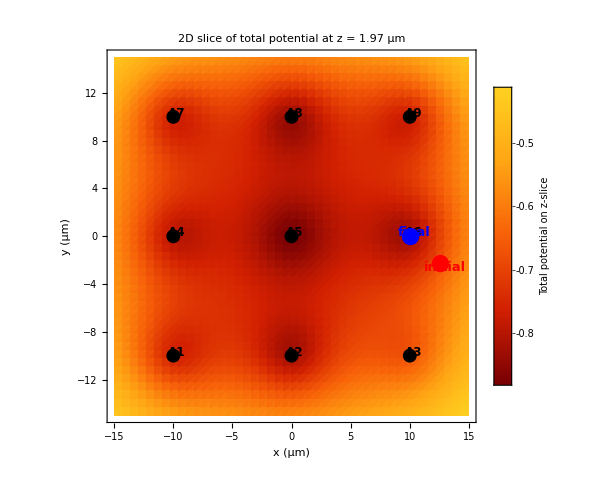

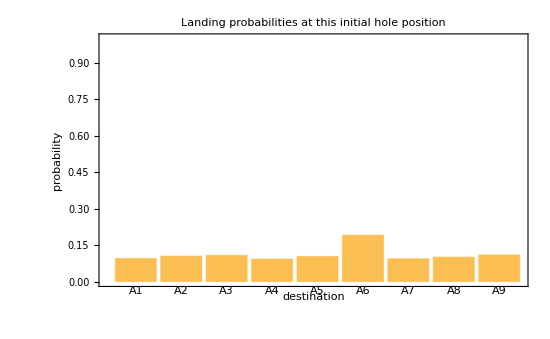

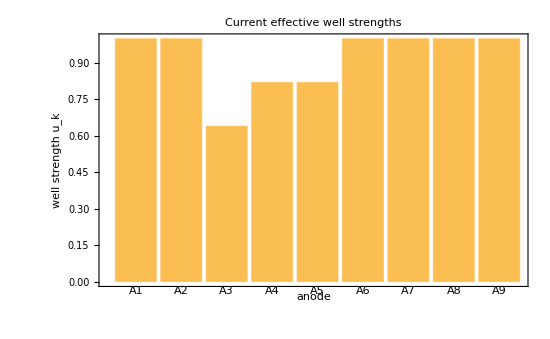

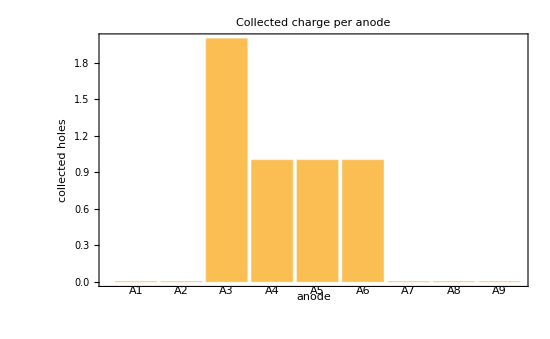

```mathematica
(* ====================================================== *)
(* 9. Per-hole diagnostics                                *)
(* ====================================================== *)

Do[
  Print[Style[Row[{"===== Charge ", i, " ====="}], 16, Bold, Blue]];
  Print["Initial position (x, y, z) in microns: ", sim["Report"][[i, "InitialPosition"]]];
  Print["Final position (x, y, z) in microns:   ", sim["Report"][[i, "FinalPosition"]]];
  Print["Choice: ", sim["Report"][[i, "Choice"]]];
  Print[sim["Report"][[i, "PotentialPlot3D"]]];
  Print[sim["Report"][[i, "RepresentativeProbabilityPlot3D"]]];
  Print[sim["Report"][[i, "PotentialSlice2D"]]];
  Print[sim["Report"][[i, "ProbabilityBarChart"]]];
  Print[sim["Report"][[i, "StrengthBar"]]];
  Print[sim["Report"][[i, "ChargeBarAfter"]]];
  ,
  {i, 1, nCharges}
];
```

```mathematica
(* ====================================================== *)
(* 10. Optional interactive viewers                       *)
(* ====================================================== *)

(* Scroll through time evolution of the 3D potential *)
potentialViewer = Manipulate[
  potentialPlot3D[
    sim["Report"][[step, "QBeforeUpdate"]],
    sim["Report"][[step, "InitialPosition"]],
    sim["Report"][[step, "FinalPosition"]],
    sim["Report"][[step, "Choice"]]
  ],
  {{step, 1, "charge step"}, 1, Length[sim["Report"]], 1}
];

(* Scroll through time evolution of 3D landing probability fields *)
probabilityViewer = Manipulate[
  probabilityMap3DForAnode[
    anodeIndex,
    sim["Report"][[step, "QBeforeUpdate"]],
    sim["Report"][[step, "InitialPosition"]],
    sim["Report"][[step, "FinalPosition"]],
    sim["Report"][[step, "Choice"]]
  ],
  {{step, 1, "charge step"}, 1, Length[sim["Report"]], 1},
  {{anodeIndex, 5, "anode"}, 1, nAnodes, 1}
];

Print[potentialViewer];
Print[probabilityViewer];
```